```mathematica
(*Run 1*)
```

0.000100985

0.938272

1.7×10^-11

0.00729753

0.1101

0.09207

5.×10^-7

0.134977

1.8×10^-7

0.13957

0.00023

0.77525

0.00013

0.782479

0.000016

1.01943

0.00013

0.00852647

0.0008

0.148117

0.000013

0.00424236

49/50

0.000016

0.493691

0.957765

6.×10^-6

0.000187285

-Graphics3D-

0.01

0.709994

0.01

0.662175

0.5

41.4029

0.745258

0.1

0.0548069

0.02

0.812522

0.236665

0.391222

0.708928

0.142829

0.0388931

-0.222852

0.0925884

0.101256

-0.00866741

21.1852

0.100716

0.00809573

5.80443×10^-7

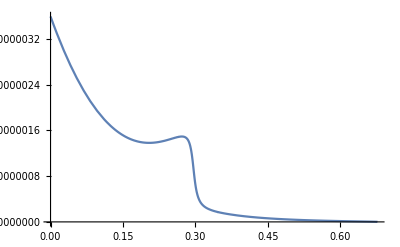

0.005

3.17×10^-6

6.8×10^-7

0.025

2.57×10^-6

3.7×10^-7

0.05

2.6×10^-6

3.3×10^-7

0.075

1.87×10^-6

2.6×10^-7

0.105

1.76×10^-6

2.4×10^-7

0.14

1.63×10^-6

2.2×10^-7

0.18

1.76×10^-6

2.2×10^-7

0.225

1.97×10^-6

2.4×10^-7

0.265

2.×10^-6

3.2×10^-7

0.295

1.07×10^-6

2.8×10^-7

0.335

3.4×10^-7

9.×10^-8

0.39

1.2×10^-7

4.×10^-8

0.53

6.×10^-8

2.×10^-8

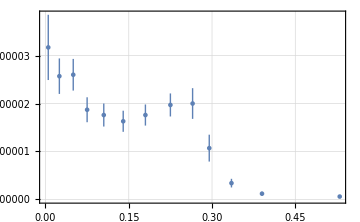

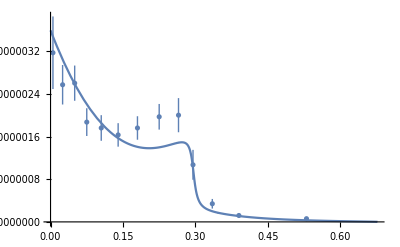

0.00898947

6.44521×10^-7

0.0034414

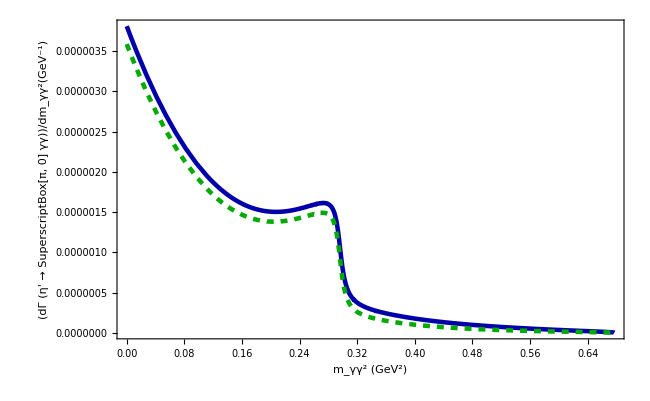

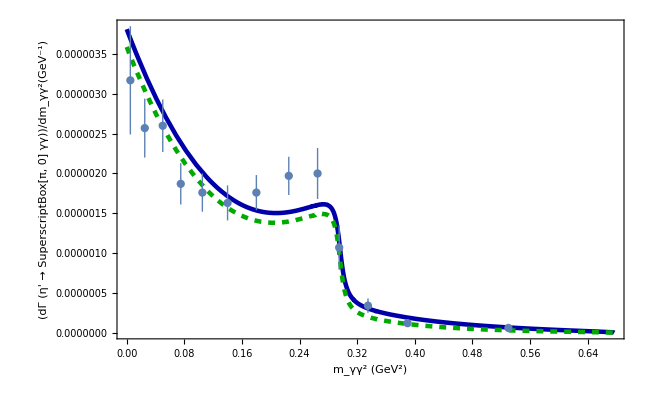

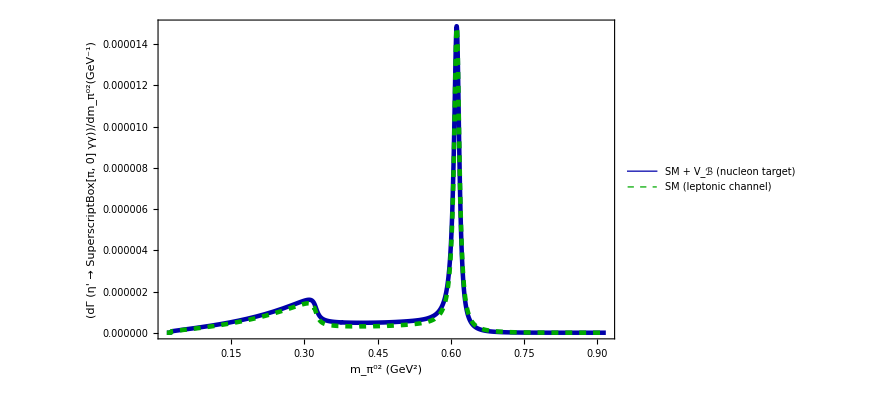

η' → π^0γγ: γγ and π^0γ Spectra  with and without V_ℬ (Nucleon Target) | 
-Graphics- | -Graphics-

EtaPrimePi0GammaGamma_1.png

0.00309925

{5.80443×10^-7,0.00309925}

{6.44521×10^-7,0.0034414}

```mathematica
GenerateValue[M0_,sigma_]:=If[sigma==0,M0,RandomVariate[NormalDistribution[M0,sigma]]]
CoupleEff = GenerateValue[0.00009474747474747476,5.255114616869139*^-6]
mN=GenerateValue[938.27208816*10^(-3),0.00000029*10^(-3)]
Δα=0.000000017*10^(-3)
α=GenerateValue[7.297525664*10^(-3),Δα]
fK =110.10*10^(-3)
fπ =92.07*10^(-3)
Δmπ=0.0005*10^(-3)
mπ=GenerateValue[134.9768*10^(-3),Δmπ]
ΔmπA=0.00018*10^(-3)
mπA=GenerateValue[139.57039*10^(-3),ΔmπA]
Δmρ=0.23*10^(-3)
mρ=GenerateValue[775.26*10^(-3),Δmρ]
Δmω=0.13*10^(-3)
mω=GenerateValue[782.66*10^(-3),Δmω]
Δmϕ=0.016*10^(-3)
mϕ=GenerateValue[1019.461*10^(-3),Δmϕ]
ΔΓω =0.13*10^(-3)
Γω = GenerateValue[8.68*10^(-3),ΔΓω]
ΔΓρ=0.8*10^(-3)
Γρ = GenerateValue[149.1*10^(-3),ΔΓρ]
ΔΓϕ=0.013*10^(-3)
Γϕ = GenerateValue[4.249*10^(-3),ΔΓϕ]
maZero = 980*10^(-3)
ΔmKP=0.016*10^(-3)
mKP=GenerateValue[493.677*10^(-3),ΔmKP]
MηPrime = GenerateValue[957.78*10^(-3),0.06*10^(-3)]
ΔΓtotal = 0.006*10^(-3)
Γtotal=GenerateValue[0.188*10^(-3),ΔΓtotal]
ΓρEff[t_] :=Γρ*((-4 mπA^2+t)/(-4 mπA^2+mρ^2))^(3/2) *HeavisideTheta[-4 mπA^2+t]
m232MAX[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-(-(-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
m232MIN[m132_] := ((MηPrime^2+mπ^2)^2)/(4 m132)-((-m132+MηPrime^2)/(2 √m132)+√(-mπ^2+((m132+mπ^2)^2)/(4 m132)))^2
Constraint[m132_, m232_]:=HeavisideTheta[m232MAX[m132]-m232]*HeavisideTheta[m232-m232MIN[m132]]
Plot3D[Constraint[m132, m232], {m132, mπ^2, MηPrime^2},{m232, mπ^2, MηPrime^2}, PlotRange->All]
Δg=0.01
g =GenerateValue[0.70,Δg]
ΔzSmBm=0.01
zSmBm =GenerateValue[0.65,ΔzSmBm]
ΔϕP=0.5
GenerateValue[41.4,ΔϕP]
ϕP = (GenerateValue[41.4,ΔϕP])Degree
ΔϕV=0.1
ϕV =(GenerateValue[3.3,ΔϕV])Degree
ΔzNS=0.02
zNS = GenerateValue[0.83,ΔzNS]
gρπγ = g/3
gρηPγ = g*zNS*Sin[ϕP]

gωπγ = g*Cos[ϕV]
gωηPγ =g/3*(zNS*Sin[ϕP]*Cos[ϕV]+2*zSmBm*Cos[ϕP]*Sin[ϕV])
gϕπγ = g*Sin[ϕV]
gϕηPγ =g/3*(zNS*Sin[ϕP]*Sin[ϕV]-2*zSmBm*Cos[ϕP]*Cos[ϕV])
cρ = gρπγ*gρηPγ
cω = gωπγ*gωηPγ
cϕ = gϕπγ*gϕηPγ
Bq2Bq2p[m132_,m232_]:=1/8 (m132^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq1Bq1[m132_,m232_]:=1/8 (m232^2+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
Bq2Bq1[m132_,m232_]:=1/8 (m132*m232+MηPrime^4) (-m132-m232+MηPrime^2+mπ^2)^2 +1/8 (-m132+MηPrime^2) (-m232+MηPrime^2) (m132 m232+MηPrime^2 (m132+m232-MηPrime^2-2 mπ^2))
BWt[m132_,m232_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)]^2
BWu[m132_,m232_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)]^2
BWtu[m132_,m232_] :=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω))]
MatrixVMD[m132_,m232_] := (Bq2Bq2p[m132,m232]*BWt[m132,m232]+2*Bq2Bq1[m132,m232]*BWtu[m132,m232] +Bq2Bq1[m132,m232]*BWu[m132,m232])*Constraint[m132, m232]
βPlusπηP[s_]:=√(1-(MηPrime+mπ)^2/s)
βMinusπηP[s_]:=√(1-(MηPrime-mπ)^2/s)
βBarPlusπηP[s_]:=√(-1+(MηPrime+mπ)^2/s)
βBarMinusπηP[s_]:=√(-1+(-MηPrime+mπ)^2/s)
βK[s_]:=√(1-(4*mKP^2)/s)
βKbar[s_]:=√((4*mKP^2)/s-1)
θπηP[s_]:= HeavisideTheta[-(MηPrime+mπ)^2+s]
BarθπηP[s_]:= HeavisideTheta[(MηPrime+mπ)^2-s]*HeavisideTheta[-(-MηPrime+mπ)^2+s]
BarBarθπηP[s_]:= HeavisideTheta[(-MηPrime+mπ)^2-s]
θK[s_]:= HeavisideTheta[-4*mKP^2+s]
θKbar[s_]:= HeavisideTheta[4*mKP^2-s]
ga0KKbarSq=((-maZero^2+mKP^2)^2)/(2 fK^2)
ga0πηPSq=((-maZero^2+MηPrime^2)^2 Sin[ϕP]^2)/fπ^2
R1[s_]:=ga0KKbarSq/(16 π^2)*(2-Log[(1+βK[s])/(1-βK[s])] *βK[s]* θK[s]-2 ArcTan[1/βKbar[s]]* βKbar[s]* θKbar[s])
R2[s_]:=ga0πηPSq/(16 π^2)*(2-((MηPrime^2-mπ^2) *Log[MηPrime/mπ])/s-Log[(βMinusπηP[s]+βPlusπηP[s])/(βMinusπηP[s]-βPlusπηP[s])]* βMinusπηP[s]* βPlusπηP[s]* θπηP[s])
R3[s_]:=ga0πηPSq/(16 π^2)*(BarBarθπηP[s]*Log[(βBarMinusπηP[s]+βBarPlusπηP[s])/(-βBarMinusπηP[s]+βBarPlusπηP[s])]*βBarMinusπηP[s]*βBarPlusπηP[s]-2*ArcTan[βMinusπηP[s]/βBarPlusπηP[s]]*BarθπηP[s]*βBarPlusπηP[s]*βMinusπηP[s])
R[s_]:=R1[s]+R2[s]+R3[s]
ImaginaryPart[s_]:=-(ga0KKbarSq* βK[s]* θK[s])/(16 π)-(ga0πηPSq* βPlusπηP[s]* βMinusπηP[s]*θπηP[s])/(16 π)
Da0[s_]:=-maZero^2+s+R[s]-R[maZero^2]+I*ImaginaryPart[s]
ALSM[s_]:=1/(2*fK*fπ)*((-MηPrime^2+s)*((-maZero^2+mKP^2)/Da0[s])*Sin[ϕP]+1/6 ((5 MηPrime^2+mπ^2-3 s)*Sin[ϕP]+√2*(4 mKP^2+MηPrime^2+mπ^2-3 s)*Cos[ϕP]))
f[z_]:=1/4* HeavisideTheta[1/4-z] *(-ⅈ π+Log[(1+√(1-4 z))/(1-√(1-4 z))])^2-ArcSin[1/(2 √z)]^2 HeavisideTheta[-1/4+z]
L[z_]:=-1/(2 z)-(2 f[1/z])/z^2
Int1VMDLSM[m132_,m232_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSM[m132_,m232_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω))+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)))]
Interference[m132_,m232_]:=2*Re[Int1VMDLSM[m132,m232]*Int2VMDLSM[m132,m232]]*Constraint[m132, m232]
LSM[m132_,m232_]:=(2*(-m132-m232+MηPrime^2+mπ^2)^2*Abs[(α ALSM[-m132-m232+MηPrime^2+mπ^2]* L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2])/mKP^2]^2)/π^2*Constraint[m132, m232]
IntegrandSM = NIntegrate[MatrixVMD[m132,m232] + Interference[m132,m232] + LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
Width = (1/2)*1/(256 MηPrime^3 π^3)*(IntegrandSM)
γγSpectrum[m122_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMD[m132,MηPrime^2+mπ^2 - m132 - m122]+Interference[m132,MηPrime^2+mπ^2 - m132 - m122]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
pTheory= Plot[γγSpectrum[m122],{m122, 0, (MηPrime-mπ)^2} , MaxRecursion->5]
p1 = (0.0 + 0.01)/2
v1 = 3.17*10^(-6)
u1 = (0.44 + 0.24)*10^(-6)
p2 = (0.01 + 0.04)/2
v2 = 2.57*10^(-6)
u2 = (0.18+0.19)*10^(-6)
p3 = (0.04 + 0.06)/2
v3 = 2.60*10^(-6)
u3 = (0.15 + 0.18)*10^(-6)
p4  = (0.06 + 0.09)/2
v4 = 1.87*10^(-6)
u4 = (0.12 +0.14)*10^(-6)
p5 = (0.09 + 0.12)/2
v5 = 1.76*10^(-6)
u5 = (0.11 + 0.13)*10^(-6)
p6 = (0.12 + 0.16)/2
v6 = 1.63*10^(-6)
u6 = (0.10 + 0.12)*10^(-6)
p7 = (0.16 + 0.20)/2
v7 = 1.76*10^(-6)
u7 = (0.09 + 0.13)*10^(-6)
p8 = (0.20 + 0.25)/2
v8 = 1.97*10^(-6)
u8 = (0.10 + 0.14)*10^(-6)
p9 = (0.25+0.28)/2
v9 = 2.00*10^(-6)
u9 = (0.17 + 0.15)*10^(-6)
p10 = (0.28 + 0.31)/2
v10 = 1.07*10^(-6)
u10 = (0.20 + 0.08)*10^(-6)
p11 = (0.31 + 0.36)/2
v11 = 0.34*10^(-6)
u11  = (0.06 + 0.03)*10^(-6)
p12 = (0.36 + 0.42)/2
v12 = 0.12 *10^(-6)
u12 = (0.03 + 0.01)*10^(-6)
p13 = (0.42 + 0.64)/2
v13 = 0.06*10^(-6)
u13  = (0.01 + 0.01)*10^(-6)
pExp=ListPlot[{{Around[p1,0],Around[v1,u1]},{Around[p2,0],Around[v2,u2]},{Around[p3,0],Around[v3,u3]},{Around[p4,0],Around[v4,u4]},{Around[p5,0],Around[v5,u5]} ,{Around[p6,0],Around[v6,u6]},{Around[p7,0],Around[v7,u7]},{Around[p8,0],Around[v8,u8]},{Around[p9,0],Around[v9,u9]}
,{Around[p10,0],Around[v10,u10]},{Around[p11,0],Around[v11,u11]},{Around[p12,0],Around[v12,u12]}
,{Around[p13,0],Around[v13,u13]}},Sequence[PlotTheme->"Detailed",ImageSize->Medium]]
Show[pTheory, pExp, PlotRange->All]
BWtDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWuDARK[m132_,m232_,Yukawa2Cs2Ms6_] := Abs[cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω]^2
BWtuDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=Re[(cρ/(-m132+mρ^2-ⅈ mρ*ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)*(cρ/(-m232+mρ^2+ⅈ mρ*ΓρEff[m232])+cϕ/(-m232+mϕ^2+ⅈ mϕ Γϕ)+cω/(-m232+mω^2+ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)]
MatrixVMDDARK[m132_,m232_,Yukawa2Cs2Ms6_] := (Bq2Bq2p[m132,m232]*BWtDARK[m132,m232,Yukawa2Cs2Ms6]+2*Bq2Bq1[m132,m232]*BWtuDARK[m132,m232,Yukawa2Cs2Ms6] +Bq2Bq1[m132,m232]*BWuDARK[m132,m232,Yukawa2Cs2Ms6])*Constraint[m132, m232]
Int1VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=(2 α)/(π*mKP^2)*L[(-m132-m232+MηPrime^2+mπ^2)/mKP^2]*ALSM[-m132-m232+MηPrime^2+mπ^2]
Int2VMDLSMDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=-Conjugate[1/4 (-m132-m232+MηPrime^2+mπ^2)^2*(m132*(cρ/(-m132+mρ^2-ⅈ mρ *ΓρEff[m132])+cϕ/(-m132+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m132+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω)+m232*(cρ/(-m232+mρ^2-ⅈ mρ *ΓρEff[m232])+cϕ/(-m232+mϕ^2-ⅈ mϕ Γϕ)+cω/(-m232+mω^2-ⅈ mω Γω)+Yukawa2Cs2Ms6*(4*64 mN^6)/α*cω))]
InterferenceDARK[m132_,m232_,Yukawa2Cs2Ms6_]:=2*Re[Int1VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]*Int2VMDLSMDARK[m132,m232,Yukawa2Cs2Ms6]]*Constraint[m132, m232]
γγSpectrumDARK[m122_,Yukawa2Cs2Ms6_] := NIntegrate[(1/2)*1/(256 MηPrime^3 π^3)*(MatrixVMDDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6]+InterferenceDARK[m132,MηPrime^2+mπ^2 - m132 - m122,Yukawa2Cs2Ms6]+LSM[m132,MηPrime^2+mπ^2 - m132 - m122])*Constraint[m132, MηPrime^2+mπ^2 - m132 - m122], {m132, mπ^2,MηPrime^2},AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->50]
IntegrandDark = NIntegrate[MatrixVMDDARK[m132,m232,CoupleEff]+InterferenceDARK[m132,m232,CoupleEff]+LSM[m132,m232], {m132, mπ^2, MηPrime^2}, {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
WidthDark = (1/2)*1/(256 MηPrime^3 π^3)*(IntegrandDark)
BranchingDark=WidthDark/Γtotal
SummaryTheory= Plot[{{γγSpectrumDARK[m122,CoupleEff]},{γγSpectrum[m122]}},{m122, 0, (MηPrime-mπ)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> None, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed],PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_γγ^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/dm_γγ^2(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650]
p1Graph=Show[SummaryTheory,pExp]
πγIn[m132_] := NIntegrate[MatrixVMD[m132,m232]+Interference[m132,m232]+LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrum[m132_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγIn[m132])
πγDark[m132_,Yukawa2Cs2Ms6_] := NIntegrate[MatrixVMDDARK[m132,m232,Yukawa2Cs2Ms6]+InterferenceDARK[m132,m232,Yukawa2Cs2Ms6]+LSM[m132,m232],  {m232, mπ^2, MηPrime^2} ,AccuracyGoal->30, Method->{"AdaptiveQuasiMonteCarlo"},MaxRecursion->100]
πγSpectrumDark[m132_,Yukawa2Cs2Ms6_]  := (1/2)*1/(256 MηPrime^3 π^3)*(πγDark[m132,Yukawa2Cs2Ms6])
Part2 = Plot[{{πγSpectrumDark[m132,CoupleEff]},{πγSpectrum[m132]}},{m132, (mπ)^2, (MηPrime)^2}, PlotRange->All,PlotStyle->{Directive[Darker[Blue], Thickness[0.005]],Directive[Darker[Green], Thickness[0.005], Dashed],Directive[Darker[Black],Thickness[0.005]],Directive[Darker[Blue],Dotted],Directive[Darker[Pink], Dashed,Thickness[0.005]],Directive[Darker[Red], Thickness[0.005]]}, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"SM + V_ℬ (nucleon target)","SM (leptonic channel)"}, LegendFunction->Framed], Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"m_(π^0)^2 (GeV^2)","(dΓ (η' →  SuperscriptBox[π, 0] γγ))/(dm_(π^0)^2)(GeV^-1)"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,Axes->False]
title=Panel[Style["η' → π^0γγ: γγ and π^0γ Spectra  with and without V_ℬ (Nucleon Target)",White,40],ImageSize->1500,Background->Blue,Alignment->Center];
DependenceVariation=Deploy@Grid[{{title,SpanFromLeft},{p1Graph,Part2}},Dividers->Gray,Spacings->{0,0}]
Export["EtaPrimePi0GammaGamma_1.png",DependenceVariation,ImageSize->5000]
BranchingTheory=Width/Γtotal
SMOutpt={Width,BranchingTheory}
OutputDark={WidthDark,BranchingDark}
```